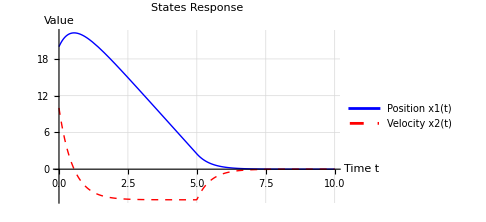
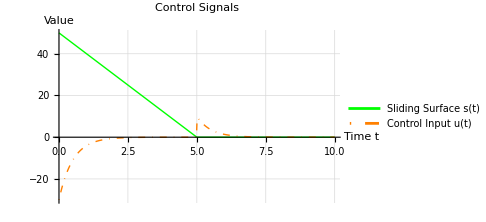
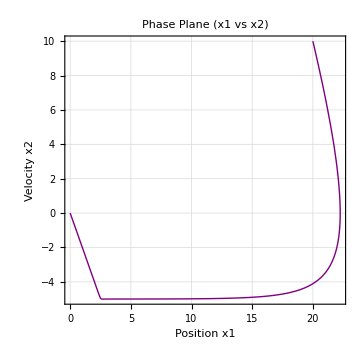
-Graphics- | -Graphics-Time Domain Responses
-Graphics-Phase Portrait

```mathematica
(*参数设置*)c=2;    (*滑动面斜率*)
k=10;    (*切换增益*)
epsilon=0.1; (*平滑参数*)
tmax=10; (*仿真时间*)

(*初始条件*)
x1init=20;
x2init=10;

(*闭环系统方程*)
eqns={x1'[t]==x2[t],x2'[t]==-c x2[t]-k Tanh[(c x1[t]+x2[t])/epsilon],x1[0]==x1init,x2[0]==x2init};

(*数值求解*)
sol=First@NDSolve[eqns,{x1,x2},{t,0,tmax}];

(*定义辅助函数*)
s[t_]:=c x1[t]+x2[t]/. sol;
u[t_]:=-c x2[t]-k Tanh[s[t]/epsilon]/. sol;

(*创建清晰的时域响应图：分开两个子图*)
plotStates=Plot[Evaluate[{x1[t],x2[t]}/. sol],{t,0,tmax},PlotStyle->{{Blue,Thick},{Red,Thick,Dashed}},PlotLabel->Style["States Response",14,Bold],AxesLabel->{"Time t","Value"},GridLines->Automatic,PlotRange->All,ImageSize->Medium,PlotLegends->Placed[{"Position x1(t)","Velocity x2(t)"},Top]];

plotControl=Plot[Evaluate[{s[t],u[t]}],{t,0,tmax},PlotStyle->{{Green,Thick},{Orange,Thick,DotDashed}},PlotLabel->Style["Control Signals",14,Bold],AxesLabel->{"Time t","Value"},GridLines->Automatic,PlotRange->All,ImageSize->Medium,PlotLegends->Placed[{"Sliding Surface s(t)","Control Input u(t)"},Top]];

(*相平面图*)
plotPhase=ParametricPlot[Evaluate[{x1[t],x2[t]}/. sol],{t,0,tmax},PlotStyle->{Thick,Purple},PlotLabel->Style["Phase Plane (x1 vs x2)",14,Bold],AxesLabel->{"Position x1","Velocity x2"},GridLines->Automatic,AspectRatio->1,Frame->True,FrameLabel->{"Position x1","Velocity x2"},ImageSize->Medium];

(*使用Grid统一布局*)
Grid[{{Labeled[Grid[{{plotStates,plotControl}}],"Time Domain Responses",Top]},{Labeled[plotPhase,"Phase Portrait",Top]}},Alignment->Center,Spacings->{1,2}]
```